```mathematica
y = Exp[-Exp[ϕ1] t] + Exp[-Exp[ϕ2] t];
ts = {1/3, 1, 3};
MM = ParametricPlot3D[y/.{t->ts},{ϕ1,-10,10},{ϕ2,-10,10}]
```

-Graphics3D-

```mathematica
v = D[y/.{ϕ1->ϕ1 + v1 τ, ϕ2->ϕ2 + v2 τ},τ]/.{τ->0} // Simplify
Avv = D[y/.{ϕ1->ϕ1 + v1 τ, ϕ2->ϕ2 + v2 τ},τ,τ]/.{τ->0} // Simplify
```

-(ⅇ^ϕ1 t^2 v1+ⅇ^ϕ2 v2)/((1+ⅇ^ϕ2+ⅇ^ϕ1 t^2)^2)

(2 (ⅇ^ϕ1 t^2 v1+ⅇ^ϕ2 v2)^2-(1+ⅇ^ϕ2+ⅇ^ϕ1 t^2) (ⅇ^ϕ1 t^2 v1^2+ⅇ^ϕ2 v2^2))/((1+ⅇ^ϕ2+ⅇ^ϕ1 t^2)^3)

```mathematica
J = Transpose[{ v/.{t->ts,v1->1, v2->0},v/.{t->ts,v1->0, v2->1}}];
J // MatrixForm
```

(-ⅇ^ϕ1/(9 (1+ⅇ^ϕ1/9+ⅇ^ϕ2)^2) | -ⅇ^ϕ2/((1+ⅇ^ϕ1/9+ⅇ^ϕ2)^2)
-ⅇ^ϕ1/((1+ⅇ^ϕ1+ⅇ^ϕ2)^2) | -ⅇ^ϕ2/((1+ⅇ^ϕ1+ⅇ^ϕ2)^2)
-(9 ⅇ^ϕ1)/((1+9 ⅇ^ϕ1+ⅇ^ϕ2)^2) | -ⅇ^ϕ2/((1+9 ⅇ^ϕ1+ⅇ^ϕ2)^2))

```mathematica
g = Transpose[J].J // Simplify;
gInv = Inverse[g] // Simplify;
```

```mathematica
a = -gInv.Transpose[J].(Avv/.{t->ts}) // Simplify;
```

```mathematica
eqs = {ϕ1''[s] == (a[[1]]/.{ϕ1->ϕ1[s], v1->ϕ1'[s],ϕ2->ϕ2[s], v2->ϕ2'[s]}),
ϕ2''[s] == (a[[2]]/.{ϕ1->ϕ1[s], v1->ϕ1'[s],ϕ2->ϕ2[s], v2->ϕ2'[s]}),
ϕ1[0] == 0, 
ϕ2[0] == 0, 
ϕ1'[0] == -1, 
ϕ2'[0] == 1};
sol = NDSolve[eqs,{ϕ1, ϕ2},{s,0,100}]
```

NDSolve::ndsz: At s == 1.40439, step size is effectively zero; singularity or stiff system suspected.

{{ϕ1→InterpolatingFunction[{{0., 1.40439}}, <>],ϕ2→InterpolatingFunction[{{0., 1.40439}}, <>]}}

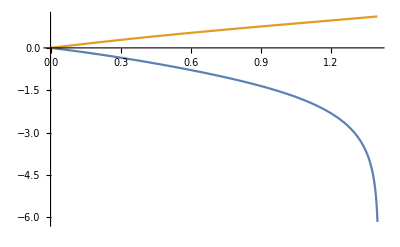

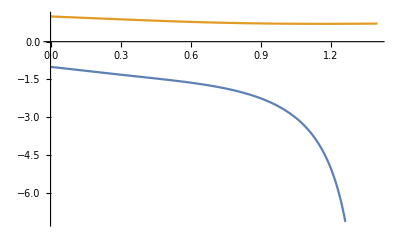

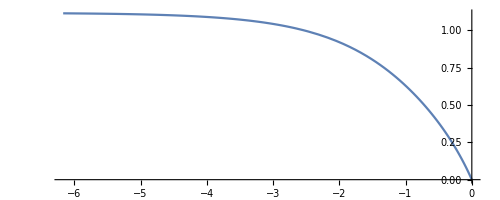

-Graphics3D-

```mathematica
smax = 1.4;
Plot[Evaluate[{ϕ1[s], ϕ2[s]}/.sol],{s,0,smax}]
Plot[Evaluate[{ϕ1'[s], ϕ2'[s]}/.sol],{s,0,smax}]
ParametricPlot[Evaluate[{ϕ1[s],ϕ2[s]}/.sol],{s,0,smax}]
Show[{MM,ParametricPlot3D[Evaluate[y/.{t->ts,ϕ1->ϕ1[s], ϕ2->ϕ2[s]}/.sol],{s,0,smax}]}]
```